```mathematica
f[x_,al_,be_]:=1/(1+1/al Exp[be x])
```

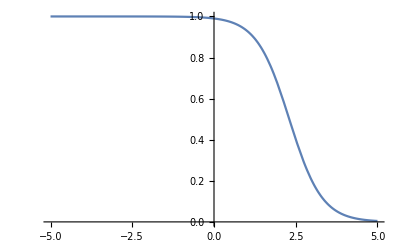

```mathematica
Plot[f[x,100,2],{x,-5,5}]
```

```mathematica
subs=FullSimplify[NSolve[{f[100,al,be]==7/8, f[600,al,be]==1/100},{al,be}, Reals]][[1]]
```

{al→25.8967,be→0.0130821}

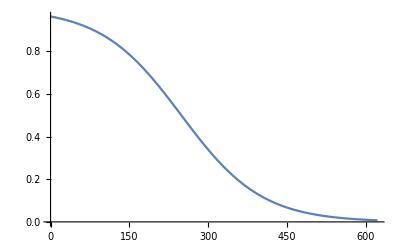

```mathematica
Plot[f[x,al,be]//.subs,{x,0,622}]
```

```mathematica
Solve[f[x,al,be]==y,x, Reals]
```

{{x→ConditionalExpression[Log[(al-al y)/y]/be,(0<y<1&&al>0)||(y>1&&al<0)||(y<0&&al<0)]}}